# Exercise 2.1 a)

### σ = -1

{{x→0,y→0}}

{0,0}

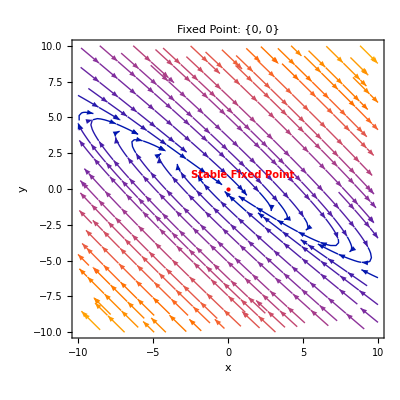

```mathematica
ClearAll["Global`*"]
f1[x_,y_,sigma_] := (sigma+3)*x+4*y
f2[x_,y_,sigma_] := -(9/4)*x+(sigma-3)*y

sol = Solve[
{f1[x,y,-1] == 0,
f2[x,y,-1] == 0} ,
{x,y}]

p1 =StreamPlot[
{f1[x,y,-1],f2[x,y,-1]},
{x,-10,10},
{y,-10,10},
AxesLabel->{"x","y"},
PlotRange->All,
StreamStyle->Blue,
Frame->True,
FrameLabel->{"x","y"}
];

fp = {x,y}/.sol[[1]]
p2=Graphics[{Red,PointSize[Large],Point[fp] }];

Show[p1,p2,
PlotLabel->"Fixed Point: "<>ToString[fp],
FontSize->14,
FontWeight->Bold,
Epilog->{Text[Style["Stable Fixed Point",Red,Bold,10],fp+{1,1}]}
]
```

### σ = 0

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→-(3 x)/4}}

{{0,0},{0,0}}

{0,0}

-(3 x)/4

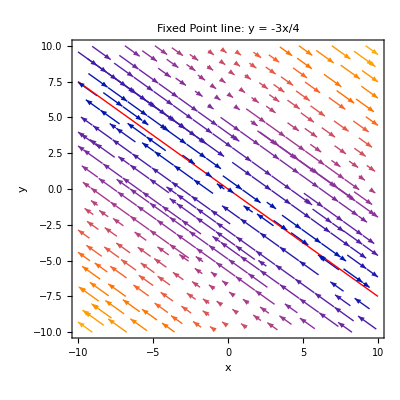

```mathematica
ClearAll["Global`*"]
f1[x_,y_,sigma_] := (sigma+3)*x+4*y;
f2[x_,y_,sigma_] := -(9/4)*x+(sigma-3)*y;

sol = Solve[
{f1[x,y,0] == 0,
f2[x,y,0] == 0},
{x,y}]

J[x_,y_] = D[{f1[x,y /. sol[[1]],0],f2[x,y /. sol[[1]],0]},{{x,y}}]

Eigenvalues[J[x,y]]
(*Both eigenvalues = 0, thus line of fixed points neither stable or unstable.*)

p1 =StreamPlot[
{f1[x,y,0],f2[x,y,0]},
{x,-10,10},
{y,-10,10},
AxesLabel->{"x","y"},
PlotRange->All,
StreamStyle->Blue,Frame->True,FrameLabel->{"x","y"}
];

fp[x_]=y /. sol[[1]]

fpPlot = Plot[fp[x],{x,-10,10},
PlotStyle->{Red,Thick},
PlotRange->Full
];

Show[p1,fpPlot,
PlotLabel->"Fixed Point line: y = -3x/4",
PlotRange->All,
FontSize->14,
FontWeight->Bold]
```

For sigma = 0, we get a line of fixed points, and since the stability matrix J and both eigenvalues are 0  we get τ = Δ = 0, thus the line of fixed points are neither stable or unstable.

### σ = -1

{{x→0,y→0}}

{0,0}

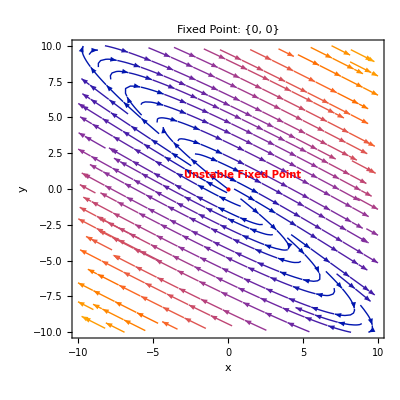

```mathematica
ClearAll["Global`*"]
f1[x_,y_,sigma_] := (sigma+3)*x+4*y
f2[x_,y_,sigma_] := -(9/4)*x+(sigma-3)*y

sol = Solve[
{f1[x,y,1] == 0,
f2[x,y,1] == 0} ,
{x,y}]

p1 =StreamPlot[
{f1[x,y,1],f2[x,y,1]},
{x,-10,10},
{y,-10,10},
AxesLabel->{"x","y"},
PlotRange->All,
StreamStyle->Blue,Frame->True,FrameLabel->{"x","y"}
];
fp = {x,y}/.sol[[1]]

p2=Graphics[
{Red,PointSize[Large],
Point[fp] }];

Show[p1,p2,
PlotLabel->"Fixed Point: "<>ToString[fp],
FontSize->14,
FontWeight->Bold,
Epilog->{Text[Style["Unstable Fixed Point",Red,Bold,10],fp+{1,1}]}
]
```